## Results of model with type II functional response

### This first section is to try single parameter combination set

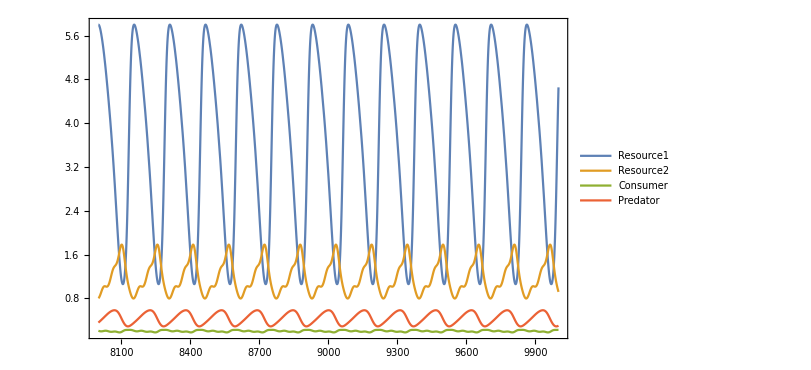

{{3.50188},{1.21831},{0.201068},{0.437608}}

```mathematica
ClearAll["Global`*"];
r1=1.71641*0.15;
K1=8.13829;
r2=1.71641*0.15;
K2=8.13829;
A=1.25;
H=0.08;
B=0.1;
S1=1.25;
h1=0.8;
e1=0.1;
S2=0.38580;
h2=0.35959;
e2=0.4;
M=0.1;
d=0.1;

α=1;
p=0.04;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==8.13829, Res2[0]==8.13829, Con[0]==0.1, Pred[0]==0.1};
s = NDSolve[eqs, {Res1,Res2, Con, Pred, q},{t,0,Tf}];
Plot[
Evaluate[{Res1[t], Res2[t], Con[t],Pred[t]}/.s],
{t,8000,10000},
PlotStyle->Automatic,
PlotLegends->{"Resource1", "Resource2", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
Table[{Res1[t]/.s, Res2[t]/.s, Con[t]/.s, Pred[t]/.s}, {t, 9000, 10000, 1}]//Mean
```

```mathematica
Export["D:\\Research\\IGP_LabExp_Public\\check\\TS_R_a10.csv",
Join[Table[Flatten[{t, Evaluate[{Res1[t], Res2[t], Con[t], Pred[t]}/.s]}],{t,0,1000}], Table[Flatten[{t, Evaluate[{Res1[t], Res2[t], Con[t], Pred[t]}/.s]}],{t,9000,10000}]]]
```

D:\Research\IGP_LabExp_Public\check\TS_R_a10.csv

#### This second section is to plot model results with fixed e2 and p values but α varying from 0 to 1

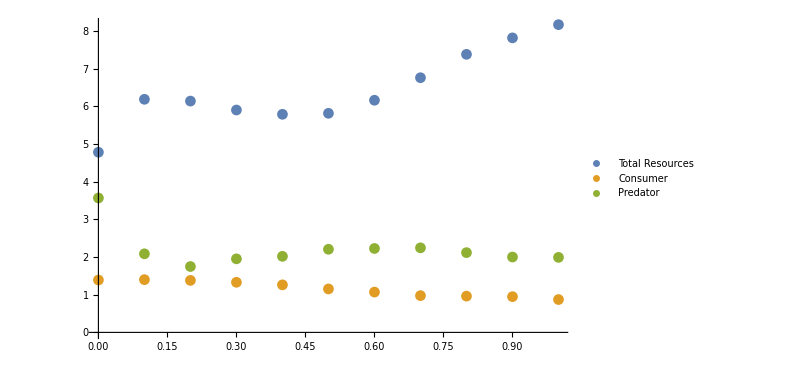

```mathematica
ClearAll["Global`*"];
r1=1.71641;
K1=8.13829;
r2=1.71641;
K2=8.13829;
A=1.25;
H=0.08;
B=0.11;
S1=1.25;
h1=0.8;
e1=0.11;
S2=0.38580;
h2=0.35959;
e2=0.4;
M=0.1;
d=0.1;

p=0.04;

Tf = 2000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==8, Res2[0]==8, Con[0]==0.1, Pred[0]==0.1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 1000, 2000, 1}]//Mean}
];
,{i, 0,1, 0.1}
]
][[2,1]];
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 11}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]},  {n,1, 11}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]},  {n,1, 11}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
(*MatrixForm[Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 21}]]*)
```

### This section is to save the results with fixed e2 and p values but α varying from 0 to 1

```mathematica
aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.2}
]
][[2,1]];
Export["K:\\IGP exp_in lab\\ProgressReport_20171115\\Type2.csv",Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 101}]];
```

### This section is to save results with e2 varying from 0 to 0.5, p varying from 0 to 0.15 and α varying from 0 to 1

```mathematica
ClearAll["Global`*"];
r1=1.71641;
K1=8.13829*1.3;
r2=1.71641;
K2=8.13829*1.3;
A=1.25;
H=0.08;
B=0.11;
S1=1.25;
h1=0.8;
e1=0.11;
S2=0.38580;
h2=0.35959;

M=0.1;
d=0.1;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};
```

```mathematica
Do[
aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
tab =  Table[
{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, 
{t, 8000, 10000, 0.01}
]//Mean;
Sow[
{i, tab}
];
,{i, 0,1, 0.2}
]
][[2,1]];
Export["E:\\Research_MonthBackup\\IGP_LabExp\\Analysis\\Type2ModResults_K_up\\Type2_e2_"<>ToString[e2*10]<>"_p_"<>ToString[p*100]<>".csv",Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1,6}]];,
{e2, 0, 0.5, 0.01},
{p, 0, 0.2, 0.01}
]
```

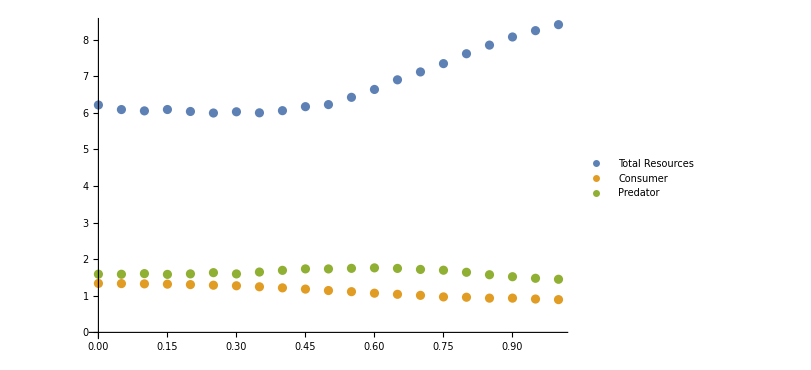

```mathematica
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 21}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]},  {n,1, 21}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]},  {n,1, 21}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
```

### Model results with type I functional response

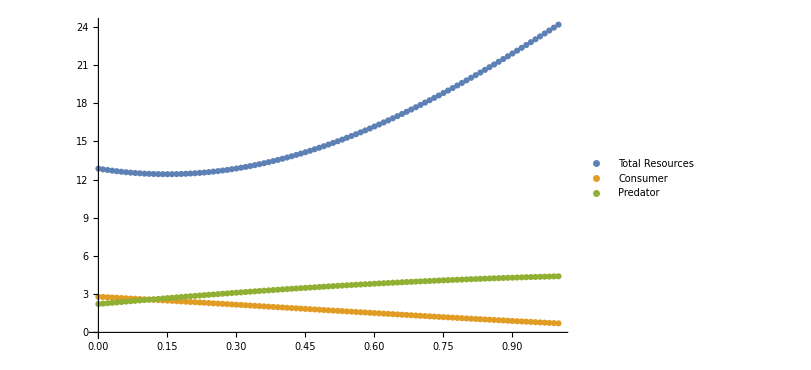

```mathematica
ClearAll["Global`*"];

r1=2.5;
K1=50;
r2=2.5;
K2=50;

A=1.0;
B=0.3;

S1=0.7;
e1=0.3;

e2=1.0;

M=1.0;
d=2.0;

p=0.75;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-A*p*Res1[t]*Con[t]-S1*(1-p)*Res1[t]*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-A*(1-p)*Res2[t]*Con[t]-S1*p*Res2[t]*Pred[t],
Con'[t]==B*A*p*Res1[t]*Con[t]+B*A*(1-p)*Res2[t]*Con[t]-M*Con[t]-α*Con[t]*Pred[t],
Pred'[t]==e1*S1*(1-p)*Res1[t]*Pred[t]+e1*S1*p*Res2[t]*Pred[t]+e2*α*Con[t]*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.01}
]
][[2,1]];
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 101}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]},  {n,1, 101}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]},  {n,1, 101}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
```

```mathematica
aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.01}
]
][[2,1]]
Export["K:\\IGP exp_in lab\\ProgressReport_20171115\\Type1.csv",Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 101}]]
```